# Example of Text Analysis

```mathematica
webpage=Import["https://writings.stephenwolfram.com/2017/11/what-is-a-computational-essay/"];
```

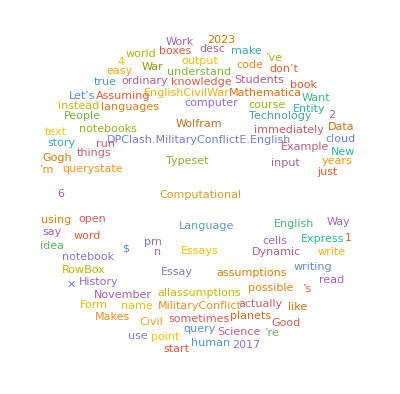

```mathematica
WordCloud[DeleteStopwords[webpage]]
```

This word cloud makes me think that this conversation is not very interesting. There seems to be no real discussion other than an assortment of people and topics

```mathematica
contents=TextContents[webpage,VerifyInterpretation->True];
```

```mathematica
counts=ReverseSort@CountsBy[contents,#Type&]
```

```mathematica
contents
```

```mathematica
persons=Normal[Select[contents,#Type==="Person"&][[All,"Interpretation"]]]
```

{Stephen Wolfram,Stephen Wolfram,Stephen Wolfram,Vincent van Gogh,Vincent van Gogh,Vincent van Gogh,Vincent van Gogh,Vincent van Gogh,Stephen Wolfram,Stephen Wolfram,Stephen Wolfram,Stephen Wolfram,Richard Crandall,Donald E. Knuth,Doug Lenat,Logic,Edward Fredkin,Stephen Wolfram,Stephen Wolfram}

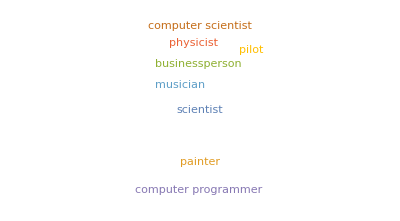

```mathematica
WordCloud[Counts[Flatten@EntityValue[persons,EntityProperty["Person","Occupation"]]]]
```

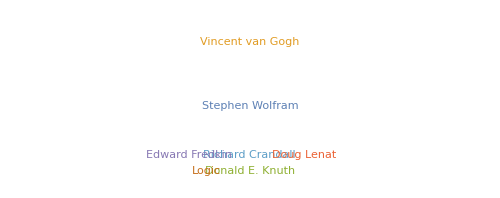

```mathematica
WordCloud[Counts[persons],ImageSize->500]
```

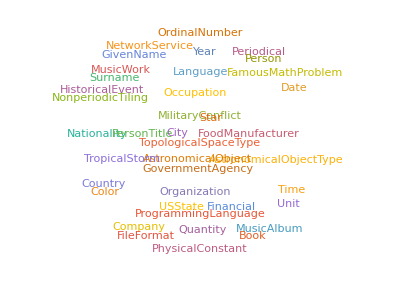

```mathematica
Show[WordCloud[counts]]
```

```mathematica
countries=Normal[Select[contents,Type==="PhysicalConstant"&][[All,"Interpretation"]]]
```

{}

```mathematica
WordCloud[countries,ImageSize->500]
```

-Graphics-

```mathematica
WordCloud[Normal[Select[contents,Type==="MilitaryConflict"&][[All,"Interpretation"]]],ImageSize->Large]
```

-Graphics-

## KeywordGraph

### Source Code

```mathematica
Options[KeywordsGraph]={DirectedEdges->False,EdgeWeight->Automatic,"LowerCase"->True,"StopWords"->True,VertexLabels->Automatic,VertexWeight->Automatic};

KeywordsGraph[text_String,number_Integer?Positive,blist_List:{},rlist_List:{},opts:OptionsPattern[{KeywordsGraph,Graph}]]:=Module[{keycounts,keywords,edges,edgeCount,data=Replace[DeleteCases[TextWords[If[TrueQ[OptionValue["StopWords"]],DeleteStopwords,Identity][If[TrueQ[OptionValue["LowerCase"]],ToLowerCase,Identity][text]]],Alternatives@@blist],rlist,{1}]},keycounts=Counts[data];Quiet[Check[keywords=TakeLargest[keycounts,number],Return[Failure["KeywordCount",<|"MessageTemplate"->"Number of specified keywords `1` exceeds the actual number of keywords `2`.","MessageParameters"->{number,Length[keycounts]}|>],Module]]];edges=Partition[Cases[data,Alternatives@@Keys[keywords]],2,1];edgeCount=If[TrueQ[Replace[OptionValue[DirectedEdges],Automatic:>False]],KeySelect[Counts[DirectedEdge@@@edges],#[[1]]!=#[[2]]&],KeySelect[Counts[Sort/@UndirectedEdge@@@edges],#[[1]]!=#[[2]]&]];Graph[Keys[keywords],Keys[edgeCount],FilterRules[Flatten[Join[{opts,VertexWeight->Replace[OptionValue[VertexWeight],Automatic:>Values[keywords]],EdgeWeight->Replace[OptionValue[EdgeWeight],Automatic:>Values[edgeCount]]},Options[KeywordsGraph]]],Options[Graph]]]]
```

### Graph Plot

```mathematica
CommunityGraphPlot[KeywordsGraph[DeleteStopwords[webpage],80,VertexSize->"VertexWeight",EdgeStyle->Directive[Black,Dashed,Opacity[0.01]]],CommunityBoundaryStyle->Directive[Red,Dashed,Opacity[0.8]],ImageSize->Large,GraphLayout->"RadialEmbedding"]
```

-Graphics-

## KeywordPlot

### Source Code

```mathematica
KeywordPlot//ClearAll;
Options[KeywordPlot]=Options[SmoothHistogram]~Join~{"PlotFunction"->Automatic,"TopN"->All};
KeywordPlot::nokwd="Keyword \"`1`\" not found in text.";

(*Operatorforms*)
KeywordPlot[keyword_String,opts:OptionsPattern[]]:=KeywordPlot[{keyword},opts];
KeywordPlot[keywords_List,opts:OptionsPattern[]]:=Function[text,KeywordPlot[text,keywords,opts]];

(*Mainform*)
KeywordPlot[text_String,keyword_String,opts:OptionsPattern[]]:=KeywordPlot[text,{keyword},opts];
KeywordPlot[text_String,keywords_List,opts:OptionsPattern[]]:=Module[{pltFun,topN,txt,kws,pos,badpos},pltFun=OptionValue["PlotFunction"]/.Automatic->SmoothHistogram;topN=OptionValue["TopN"];txt=RemoveDiacritics@ToLowerCase@text;kws=RemoveDiacritics@ToLowerCase@keywords;pos=StringPosition[txt,#][[All,1]]&/@kws;badpos=Position[pos,{}];If[badpos=!={},ResourceFunction["ResourceSystemMessage"][KeywordPlot::nokwd,#]&/@Extract[kws,badpos];If[Flatten[pos]=={},Return@$Failed,(*nokeywordstoplot*)kws=Delete[kws,badpos];pos=Delete[pos,badpos];]];If[IntegerQ@topN,ord=OrderingBy[pos,-Length[#]&];pos=Take[pos[[ord]],UpTo@topN];kws=Take[kws[[ord]],UpTo@topN];];pltFun@@{pos,Sequence@@FilterRules[{opts},Options[pltFun]],PlotLegends->kws,AspectRatio->1/GoldenRatio,PlotTheme->"Minimal",ImageSize->Automatic,Frame->None}]
```

### Code

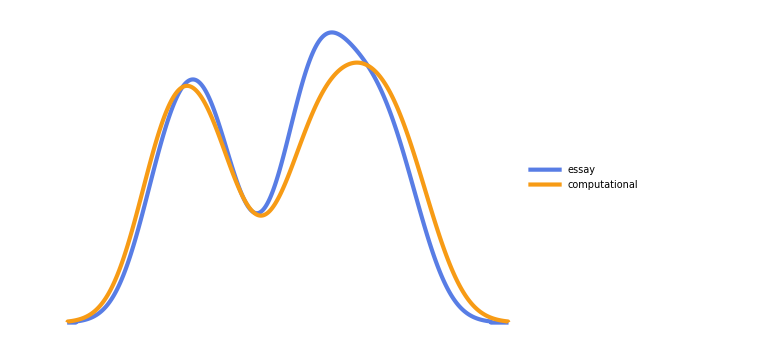

```mathematica
keywords={"essay","computational"};

KeywordPlot[keywords,ImageSize->Large,PlotLegends->Placed[keywords,{{.15,.8}}],PlotTheme->"Business"]@webpage
```

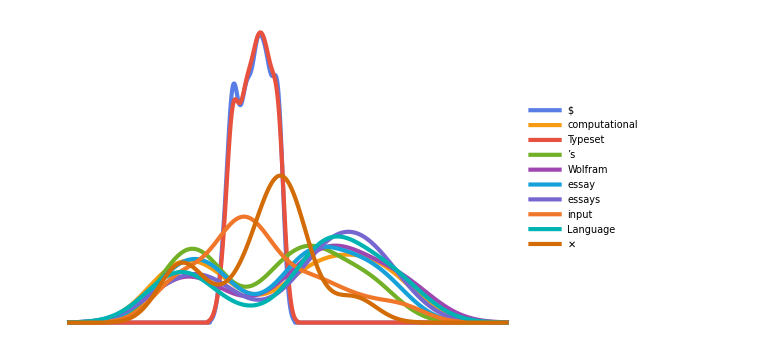

```mathematica
KeywordPlot[Normal[Keys[TakeLargest[Counts[TextCases[DeleteStopwords[webpage],"Word"]],10]]],ImageSize->Large,PlotLegends->Placed[Normal[Keys[TakeLargest[Counts[TextCases[DeleteStopwords[webpage],"Word"]],10]]],{{.15,.8}}],PlotTheme->"Business"]@webpage
```

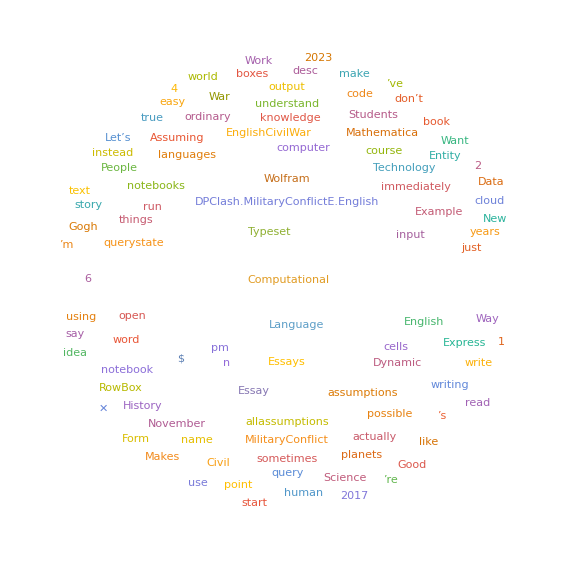

```mathematica
WordCloud[DeleteStopwords[webpage],ImageSize->Large]
```

# Resource Functions

```mathematica
ResourceFunction["ReadabilityScore"][webpage]
```

11.6548

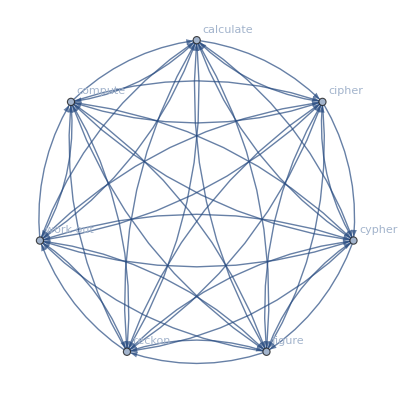

```mathematica
ResourceFunction["SynonymGraph"]["compute",1,ImageSize->Full]
```